```mathematica
Uzl={0.1, 0.2, 0.3, 0.4};
Znach={-1.087, 2.054, -5.909, 8.872};
n=Length[Uzl]-1;
Do[{Subscript[x, i]=Uzl[[i+1]], Subscript[y, i]=Znach[[i+1]]},{i, 0, n}]
ε= 1/2*10^-3; 
m=1;
Do[Subscript[t, i]= ∑_(k=0)^n Subscript[x, k]^i, {i,0,2m}];
Do[Subscript[c, i]=∑_(k=0)^n Subscript[y, k] Subscript[x, k]^i, {i, 0, m}];
eqv=Table[∑_(i=0)^m Subscript[α, i] Subscript[t, i+k]==Subscript[c, k], {k, 0, m}];
Koef=Solve[eqv, {}]//Flatten
```

{α_0→-4.496,α_1→21.914}

```mathematica
P[x_]=(∑_(i=0)^m Subscript[α, i]*x^i)/.Koef
Tbl=Table[{Subscript[x, k], Subscript[y, k]}, {k, 0, n}];
Fun=Table[x^i, {i, 0, m}];
P1[x_]=Fit[Tbl, Fun, x]//Flatten
P[x]==P1[x]
```

-4.496+21.914 x

-4.496+21.914 x

True

```mathematica
δ=√((1/(n+1))*∑_(k=-0)^n (P[Subscript[x, k]]-Subscript[y, k])^2)  //N 
δ<ε
```

4.77332

False

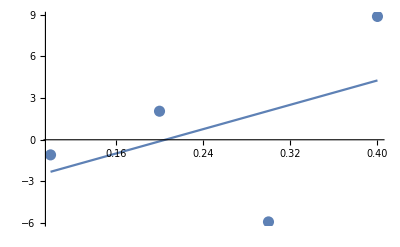

```mathematica
Gr1=ListPlot[Tbl, PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x], {x, Subscript[x, 0], Subscript[x, n]}];
Show[Gr1, Gr2]
```

```mathematica
m=2;
Do[Subscript[t, i]= ∑_(k=0)^n Subscript[x, k]^i, {i,0,2m}];
Do[Subscript[c, i]=∑_(k=0)^n Subscript[y, k] Subscript[x, k]^i, {i, 0, m}];
eqv=Table[∑_(i=0)^m Subscript[α, i] Subscript[t, i+k]==Subscript[c, k], {k, 0, m}];
Koef=Solve[eqv, {}]//Flatten

P[x_]=(∑_(i=0)^m Subscript[α, i]*x^i)/.Koef
```

{α_0→10.054,α_1→-123.586,α_2→291.}

10.054-123.586 x+291. x^2

```mathematica
Tbl=Table[{Subscript[x, k], Subscript[y, k]}, {k, 0, n}];
Fun=Table[x^i, {i, 0, m}];
P1[x_]=Fit[Tbl, Fun, x]//Flatten
P[x]==P1[x]
```

10.054-123.586 x+291. x^2

10.054-123.586 x+291. x^2==10.054-123.586 x+291. x^2

```mathematica
δ=√((1/(n+1))*∑_(k=-0)^n (P[Subscript[x, k]]-Subscript[y, k])^2)  //N 
δ<ε
k1=δ/ε
```

3.78432

False

7568.64

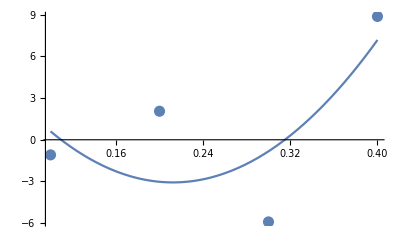

```mathematica
Gr1=ListPlot[Tbl, PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x], {x, Subscript[x, 0], Subscript[x, n]}];
Show[Gr1, Gr2]
```

```mathematica
(*_____________________*)


m=3;
Do[Subscript[t, i]= ∑_(k=0)^n Subscript[x, k]^i, {i,0,2m}];
Do[Subscript[c, i]=∑_(k=0)^n Subscript[y, k] Subscript[x, k]^i, {i, 0, m}];
eqv=Table[∑_(i=0)^m Subscript[α, i] Subscript[t, i+k]==Subscript[c, k], {k, 0, m}];
Koef=Solve[eqv, {}]//Flatten

P[x_]=(∑_(i=0)^m Subscript[α, i]*x^i)/.Koef
```

{α_0→-49.18,α_1→818.517,α_2→-3940.,α_3→5641.33}

-49.18+818.517 x-3940. x^2+5641.33 x^3

```mathematica
Tbl=Table[{Subscript[x, k], Subscript[y, k]}, {k, 0, n}];
Fun=Table[x^i, {i, 0, m}];
P1[x_]=Fit[Tbl, Fun, x]//Flatten
P[x]==P1[x]
```

-49.18+818.517 x-3940. x^2+5641.33 x^3

-49.18+818.517 x-3940. x^2+5641.33 x^3==-49.18+818.517 x-3940. x^2+5641.33 x^3

```mathematica
δ=√((1/(n+1))*∑_(k=-0)^n (P[Subscript[x, k]]-Subscript[y, k])^2)  //N 
δ<ε
k2=ε/δ
```

6.57771×10^-12

True

7.60143×10^7

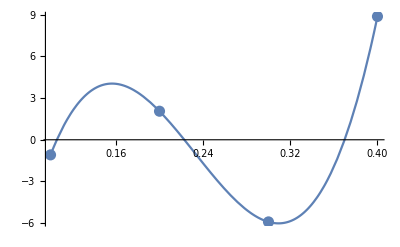

```mathematica
Gr1=ListPlot[Tbl, PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x], {x, Subscript[x, 0], Subscript[x, n]}];
Show[Gr1, Gr2]
```